# Multivariable Function Visualization in Mathematica

Christopher Hanusa
http://qc.edu/~chanusa
chanusa@qc.cuny.edu

## Plot / Plot3D

To plot the graph of a function y=f(x), use the Plot command.  This command has the same type of structure as the Table command.

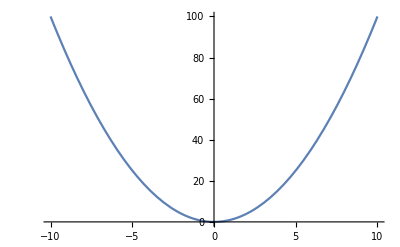

```mathematica
Plot[x^2,{x,-10,10}]
```

You give the function you want to graph, the variable that is changing, along with its domain.

To plot the graph of a function z=f(x,y), use the Plot3D command.

```mathematica
Plot3D[x^2+y^2,{x,-5,5},{y,-5,5}]
```

-Graphics3D-

2D and 3D graphics are different types of objects and can not be combined.

## RegionPlot3D for blocks with interesting top surfaces

### Parabolic Bowl

```mathematica
bowlblock=RegionPlot3D[x^2+y^2>z,{x,-1,1},{y,-1,1},{z,-.5,3}]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"Bowl.stl",bowlblock]
```

### Sinusoidal Plot

```mathematica
block=RegionPlot3D[Sin[x]+Sin[y]>z,{x,0-Pi/2,6Pi-Pi/2},{y,0-Pi/2,6Pi-Pi/2},{z,-3,3}]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"Bumpy.stl",block]
```

## Use PlotPoints!

That’s not nearly as smooth as we would like it, and that is because Mathematica is not sampling many points in the range.  We can specify that Mathematica should choose a certain number of points in each direction using the PlotPoints option.

```mathematica
block2=RegionPlot3D[Sin[x]+Sin[y]>z,{x,0-Pi/2,6Pi-Pi/2},{y,0-Pi/2,6Pi-Pi/2},{z,-3,3},PlotPoints->{100,100,100}]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"Bumpy.HD.stl",block2]
```

## Extrusion for thickening surfaces

There is a hidden option called Extrusion that allows you to thicken surfaces in order to be able to print them.

```mathematica
bowl=Plot3D[x^2+y^2,{x,-5,5},{y,-5,5},Extrusion->1]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"bowl.stl",bowl]
```

```mathematica
Import[NotebookDirectory[]<>"bowl.stl"]
```

-Graphics3D-

Notice that the aspect ratio of Mathematica’s default rendering is not the same as the natural 1-1-1 aspect ratio.  We can fix this with a BoxRatios option

```mathematica
bowl=Plot3D[x^2+y^2,{x,-5,5},{y,-5,5},Extrusion->1,BoxRatios->Automatic]
```

-Graphics3D-

We can use some simple math to adjust the surface.  Scale it down by a factor of 2 and cut off the box to have height 10.

```mathematica
bowl=Plot3D[1/2(x^2+y^2),{x,-5,5},{y,-5,5},Extrusion->1,BoxRatios->Automatic,PlotRange->{{-5,5},{-5,5},{-1,10}}]
```

-Graphics3D-

In order to get rid of the gray bits, we need to use the option ClippingStyle.

```mathematica
bowl=Plot3D[1/2(x^2+y^2),{x,-5,5},{y,-5,5},Extrusion->.5,BoxRatios->Automatic,PlotRange->{{-5,5},{-5,5},{-1,10}},ClippingStyle->None]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"betterbowl.stl",bowl]
```

```mathematica
Import[NotebookDirectory[]<>"betterbowl.stl"]
```

-Graphics3D-

Again, use PlotPoints to make it smoother.

```mathematica
bowl=Plot3D[1/2(x^2+y^2),{x,-5,5},{y,-5,5},Extrusion->.5,BoxRatios->Automatic,PlotRange->{{-5,5},{-5,5},{-1,10}},ClippingStyle->None,PlotPoints->100]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"betterbowl.HD.stl",bowl]
```

## Plotting curves

For a vector function of the form r(t)=<x(t),y(t),z(t)>, use ParametricPlot3D with the option PlotStyle->Tube[].

```mathematica
ParametricPlot3D[{Sin[t],Sin[2t],Sin[3t]},{t,0,2Pi},PlotStyle->Tube[.1],PlotRange->All]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"Curve.stl",%]
```

Make the tube nicer by adding in PlotPoints options into both the ParametricPlot3D function and the PlotStyle option (for the radial component).

```mathematica
ParametricPlot3D[{Sin[t],Sin[2t],Sin[3t]},{t,0,2Pi},PlotStyle->Tube[.1,PlotPoints->50],PlotRange->All,PlotPoints->100]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"Curve.HD.stl",%]
```